# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

Shoulder potential

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"anharm_chains_shoulder.m";
```

## Import initial data

```mathematica
(* load position data from disk *)
Subscript[r, data,0]=Import["collision_test_field_r0.dat","Real64"]
```

{0.930552,1.89397,2.06271,1.85097,1.86486,0.911984,1.66951,0.815439}

```mathematica
(* length L should be conserved *)
Total[Subscript[r, data,0]]
```

12.

```mathematica
Subscript[q, data,0]=Most[Accumulate[Prepend[Subscript[r, data,0],0]]]
Length[%]
```

{0,0.930552,2.82452,4.88724,6.7382,8.60306,9.51505,11.1846}

8

```mathematica
(* check *)
Norm[FieldDifferences[Subscript[q, data,0],Total[Subscript[r, data,0]]]-Subscript[r, data,0]]
```

1.51007×10^-15

```mathematica
(* load momentum data from disk *)
Subscript[p, data,0]=Import["collision_test_field_p0.dat","Real64"]
```

{0.376258,0.131313,-0.244379,1.17169,-0.464796,0.213526,-0.738634,-0.444979}

```mathematica
(* total momentum is zero by convention *)
Total[Subscript[p, data,0]]
```

2.77556×10^-16

```mathematica
Subscript[V, pot]={1/2,1,1};
```

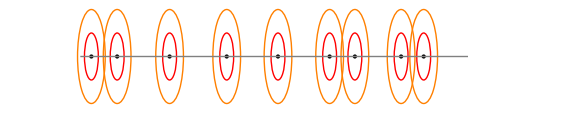

```mathematica
VisualizeField[Accumulate[Prepend[Subscript[r, data,0],0.4]],Subscript[V, pot],14]
```

```mathematica
(* without collision detection *)
Animate[VisualizeField[Subscript[q, data,0]+0.4+t Subscript[p, data,0],Subscript[V, pot],12],{t,0,10},AnimationRunning->False]
```

## Run simulation

```mathematica
(* example *)
PredictCollision[1.2,-1.6,{1/2,1,1}]
PredictCollision[1.2,-2.6,{1/2,1,1}]
```

{1,1.6,0.125,PlatBounce}

{1,-1.66132,0.0769231,PlatIn}

```mathematica
(* example *)
NextCollision[Subscript[r, data,0],Subscript[p, data,0],Subscript[V, pot]]
```

{1,2.16204,0.224735,PlatOut,8}

```mathematica
(* example *)
CollisionInfo[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot]]
```

{0.224735,PlatOut,8,{0.670403,0.476965}}

```mathematica
(* example *)
UpdateField[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot]]
Differences[First[%]]
```

{{0.0845583,0.960062,2.7696,5.15056,6.63375,8.65105,9.34905,11.0846},{1.04666,0.131313,-0.244379,1.17169,-0.464796,0.213526,-0.738634,-1.11538},0.224735}

{0.875504,1.80954,2.38095,1.48319,2.0173,0.698001,1.73551}

```mathematica
Subscript[f, seq]=FieldSequence[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot],32];
```

```mathematica
(* example *)
Subscript[f, seq]⟦{1,2,-1}⟧
```

{{{0,0.930552,2.82452,4.88724,6.7382,8.60306,9.51505,11.1846},{0.376258,0.131313,-0.244379,1.17169,-0.464796,0.213526,-0.738634,-0.444979},0},{{0.0845583,0.960062,2.7696,5.15056,6.63375,8.65105,9.34905,11.0846},{1.04666,0.131313,-0.244379,1.17169,-0.464796,0.213526,-0.738634,-1.11538},0.224735},{{0.237709,1.25184,3.69071,4.76865,5.76865,8.13118,9.96863,10.8658},{-0.385959,-0.244379,0.522367,-0.738634,1.57406,1.04666,-0.427401,-1.34672},4.38939}}

```mathematica
Interpolation[{Last[#],First[#]}&/@Subscript[f, seq],InterpolationOrder->1]
Animate[VisualizeField[%[t],Subscript[V, pot],12],{t,0,4},AnimationRunning->False]
```

InterpolatingFunction[{{0., 4.38939}}, <>]

## Compare with C implementation

```mathematica
"collision_test_event_";
Subscript[coll, test]=Transpose[{(* event times *)Import[%<>"time.dat","Real64"],(* event types *) Import[%<>"type.dat","Integer32"]/.{0->PlatIn,1->PlatOut,2->PlatBounce,3->Core},(* particle indices *)Import[%<>"iprt.dat","Integer32"]+1}]
```

{{0.224735,PlatOut,8},{0.432684,Core,6},{0.519996,PlatBounce,4},{0.634966,Core,1},{0.927199,PlatBounce,7},{1.11385,PlatBounce,5},{1.14263,PlatBounce,2},{1.28898,Core,6},{1.5076,PlatOut,6}}

```mathematica
Most[CollisionInfo[AdvanceField[#,0.0001],Total[Subscript[r, data,0]],Subscript[V, pot]]]&/@Subscript[f, seq]⟦1;;9⟧
(* compare *)
Norm[%-Subscript[coll, test]]
```

{{0.224735,PlatOut,8},{0.432684,Core,6},{0.519996,PlatBounce,4},{0.634966,Core,1},{0.927199,PlatBounce,7},{1.11385,PlatBounce,5},{1.14263,PlatBounce,2},{1.28898,Core,6},{1.5076,PlatOut,6}}

3.75553×10^-15

```mathematica
(* reference *)
Subscript[coll, ref]=Most[CollisionInfo[AdvanceField[#,0.0001],Total[Subscript[r, data,0]],Subscript[V, pot]]]&/@Subscript[f, seq]⟦1;;9⟧
```

{{0.224735,PlatOut,8},{0.432684,Core,6},{0.519996,PlatBounce,4},{0.634966,Core,1},{0.927199,PlatBounce,7},{1.11385,PlatBounce,5},{1.14263,PlatBounce,2},{1.28898,Core,6},{1.5076,PlatOut,6}}

```mathematica
(* save to disk for comparison *)
"collision_test_ref_event_";
{(* event times *)Export[%<>"time.dat",Subscript[coll, ref]⟦;;,1⟧,"Real64"],(* event types *) Export[%<>"type.dat",Subscript[coll, ref]⟦;;,2⟧/.{PlatIn->0,PlatOut->1,PlatBounce->2,Core->3},"Integer32"],(* particle indices *)Export[%<>"iprt.dat",Subscript[coll, ref]⟦;;,3⟧-1,"Integer32"]};
```